```mathematica
ClearAll["Global`*"];
Remove["Global`*"];
Off[RuleDelayed::rhs];
PrependTo[$Path,"/home/sounak/physics/codes/"];
<<autoPSG`
```

Remove::rmnsm: There are no symbols matching "Global`*".

```mathematica
SeparatePowers=With[{VPower=Verbatim[Power],VPlus=Verbatim[Plus],VTimes=Verbatim[Times]},{VPower[VTimes[a__],b_]:>Inactive[Times]@@((Power[#,b]&)/@(List[a])),VPower[VPower[a_,b_],c_]:>Power[a,Times[b,c]],VPower[a__,VPlus[b__]]:>Inactive[Times]@@((Power[a,#]&)/@List[b]),VPower[a_,VTimes[c__/;MemberQ[List[c],VPlus,{2},Heads->True]]]:>Power[a,Distribute[Times[c]]],VPower[a_,VPlus[VTimes[c__/;MemberQ[List[c],VPlus,{2},Heads->True]],b__]]:>Power[a,Map[Distribute,Plus[b,Times[c]],Infinity]]}];

z2rules={η[x_]^Times[j_?Negative,k_]->η[x]^(-k j),η[x_]^Times[j_?EvenQ,m_:1]->1,η[x_]^Times[j_?OddQ,m_:1]->η[x]^(m),η[x_]^Power[j_,n_]->η[x]^j};
SeparateAndApplyZ2[expr_]:=(expr//.SeparatePowers//.z2rules//.{Inactive[Times]->Times});
z2Simplify[expr_]:=FixedPoint[SeparateAndApplyZ2,expr];
```

```mathematica
SGSet//Column
```

Tx^-1·Ty^-1·Tx·Ty=e
Pxy^-1·Tx^-1·Pxy·Ty=e
R^-1·Tx·R·Ty=e
Pxy·Pxy=e
Tx^-1·Ty^-1·R^-1·Ty·R=e
R·R·R·R·R·R=e
R·Pxy·R·Pxy=e

```mathematica
{{Tx^-1·Ty^-1·Tx·Ty=e}, {Pxy^-1·Tx^-1·Pxy·Ty=e}, {R^-1·Tx·R·Ty=e}, {Pxy·Pxy=e}, {Tx^-1·Ty^-1·R^-1·Ty·R=e}, {R·R·R·R·R·R=e}, {R·Pxy·R·Pxy=e}}
```

e
e
e
e
e
e
e

```mathematica
f
```

```mathematica
rules=getInvRules[{x,x+y}]
```

{x→x,y→-x+y}

```mathematica
{x,x+y}/.rules
```

{x,y}

```mathematica
initPSGSolverZ2[];
rels=MatrixRelationsZ2[SGSet];
Values[FAssoc];
freds;
Values[MAssoc]//Column;
rels=decomposeGtoFMZ2[rels];
rels1=rels;
rules0=DeleteCases[Join[Values[FAssoc],Values[MAssoc]],Null];
rels1=ApplyRules[rels1,rules0];
Print["apply the following rules:"];
Column[rules0]
Print["To Equations:"];
Column[rels1]
Print["To get:"];
Column[rels1]
Print["relabel to get:"];
rels1=relabelIndices/@rels1;
Column[rels1]
Print["MF separatoin to get"];
rels1=Join@@(SplitEqMF/@rels1);
Column[rels1]
elementaryFReductions=Join@@(ReduceF/@rels1);
freds=Join[freds,elementaryFReductions];
composedFReductions=FReductions2[elementaryFReductions];
Scan[(AssociateTo[FAssoc,#->composedFReductions[#]]&),Keys[composedFReductions]];
Print["Solvers give us:"];
rules0=DeleteCases[Join[Values[FAssoc],Values[MAssoc]],Null];
Column[rules0]

rels1=ApplyRules[rels1,rules0];
Print["Applying, we have:"];
Column[rels1]
rels1=reduceEtas[rels1];
Print["applying these and the following etas:"];
Print[etaAssoc];
Print["give us:"];
Column[rels1]

rels2=Join@@(SplitEqMF/@rels1);
Print["split:"];
Column[rels2]
rels2=substAllMsIntoAllEqs[rels2]//z2Simplify;
Print["M subst:"];
Column[rels2]
rels2=Join@@(SplitFxy/@rels2);
Print["split x y"];
Column[rels2]
rels2=relabelIndices/@rels2;
Print[" after relabelling"];
Column[rels2]

elementaryFReductions=Join@@(ReduceF/@rels2);
freds=Join[freds,elementaryFReductions];
composedFReductions=FReductions2[elementaryFReductions];
Scan[(AssociateTo[FAssoc,#->composedFReductions[#]]&),Keys[composedFReductions]];
Column[Values[FAssoc]]
rules0=DeleteCases[Join[Values[FAssoc],Values[MAssoc]],Null];
Print["final rules"];
Column[rules0]
Print["to rels"];
Column[rels2]
rels2=ApplyRules[rels2,rules0];
Print["To Get"];
Column[rels2]
rels2=reduceEtas[rels2];
Column[rels2]
Column[Values[FAssoc]]



(*elementaryFReductions=Join@@(ReduceF/@rels1);
composedFReductions=FReductions[elementaryFReductions];*)

(*rels2=phaseSolverIterate[rels];
rels2=matrixSolverIterate[rels2];
Column[%]
Values[FAssoc]//Column
Values[MAssoc]//Column*)
```

apply the following rules:

F_Tx[x_,y_]→1
F_Ty[x_,y_]→η_1^x
M_Tx→τ_0
M_Ty→τ_0

To Equations:

F_Pxy[1+y,x] F_Pxy^-1[y,x]=η_1^x η_2
F_R[-1+x-y,x] F_R^-1[x-y,x]=η_1^x η_3
M_Pxy·M_Pxy F_Pxy[x,y] F_Pxy[y,x]=η_4
F_R[x-y,x] F_R^-1[x-y,1+x]=η_1^(1+y) η_5
M_R·M_R·M_R·M_R·M_R·M_R F_R[-x,-y] F_R[x,y] F_R[x-y,x] F_R[-y,x-y] F_R[y,-x+y] F_R[-x+y,-x]=η_6
M_R·M_Pxy·M_R·M_Pxy F_Pxy[y,x] F_Pxy[y,-x+y] F_R[x,y] F_R[-x+y,y]=η_7

To get:

F_Pxy[1+y,x] F_Pxy^-1[y,x]=η_1^x η_2
F_R[-1+x-y,x] F_R^-1[x-y,x]=η_1^x η_3
M_Pxy·M_Pxy F_Pxy[x,y] F_Pxy[y,x]=η_4
F_R[x-y,x] F_R^-1[x-y,1+x]=η_1^(1+y) η_5
M_R·M_R·M_R·M_R·M_R·M_R F_R[-x,-y] F_R[x,y] F_R[x-y,x] F_R[-y,x-y] F_R[y,-x+y] F_R[-x+y,-x]=η_6
M_R·M_Pxy·M_R·M_Pxy F_Pxy[y,x] F_Pxy[y,-x+y] F_R[x,y] F_R[-x+y,y]=η_7

relabel to get:

F_Pxy[x,y] F_Pxy^-1[-1+x,y]=η_1^y η_2
F_R[x,y] F_R^-1[1+x,y]=η_1^y η_3
M_Pxy·M_Pxy F_Pxy[x,y] F_Pxy[y,x]=η_4
F_R[x,y] F_R^-1[x,1+y]=η_1^(1-x+y) η_5
M_R·M_R·M_R·M_R·M_R·M_R F_R[-x,-y] F_R[x,y] F_R[x-y,x] F_R[-y,x-y] F_R[y,-x+y] F_R[-x+y,-x]=η_6
M_R·M_Pxy·M_R·M_Pxy F_Pxy[y,x] F_Pxy[y,-x+y] F_R[x,y] F_R[-x+y,y]=η_7

MF separatoin to get

F_Pxy[x,y] F_Pxy^-1[-1+x,y]=η_1^y η_2
F_R[x,y] F_R^-1[1+x,y]=η_1^y η_3
M_Pxy·M_Pxy F_Pxy[x,y] F_Pxy[y,x]=η_4
F_R[x,y] F_R^-1[x,1+y]=η_1^(1-x+y) η_5
M_R·M_R·M_R·M_R·M_R·M_R F_R[-x,-y] F_R[x,y] F_R[x-y,x] F_R[-y,x-y] F_R[y,-x+y] F_R[-x+y,-x]=η_6
M_R·M_Pxy·M_R·M_Pxy F_Pxy[y,x] F_Pxy[y,-x+y] F_R[x,y] F_R[-x+y,y]=η_7

Solvers give us:

F_Tx[x_,y_]→1
F_Ty[x_,y_]→η_1^x
F_R[x_,y_]→η_1^(1/2 (-1-y) y) (η_1^y η_3)^-x η_5^-y
F_Pxy[x_,y_]→(η_1^y η_2)^x F_Pxy[0,y]
M_Tx→τ_0
M_Ty→τ_0

Applying, we have:

M_Pxy·M_Pxy F_Pxy[0,x] F_Pxy[0,y]=η_2^(x+y) η_4
M_R·M_R·M_R·M_R·M_R·M_R=η_6
M_R·M_Pxy·M_R·M_Pxy F_Pxy[0,x] F_Pxy[0,-x+y]=η_3^y η_7

applying these and the following etas:

<||>

give us:

M_Pxy·M_Pxy F_Pxy[0,x] F_Pxy[0,y]=η_2^(x+y) η_4
M_R·M_R·M_R·M_R·M_R·M_R=η_6
M_R·M_Pxy·M_R·M_Pxy F_Pxy[0,x] F_Pxy[0,-x+y]=η_3^y η_7

split:

F_Pxy[0,x] F_Pxy[0,y]=η_2^(x+y)
M_Pxy·M_Pxy=η_4
M_R·M_R·M_R·M_R·M_R·M_R=η_6
F_Pxy[0,x] F_Pxy[0,-x+y]=η_3^y
M_R·M_Pxy·M_R·M_Pxy=η_7

M subst:

F_Pxy[0,x] F_Pxy[0,y]=η_2^(x+y)
M_Pxy·M_Pxy=η_4
M_R·M_R·M_R·M_R·M_R·M_R=η_6
F_Pxy[0,x] F_Pxy[0,-x+y]=η_3^y
M_R·M_Pxy·M_R·M_Pxy=η_7

split x y

F_Pxy[0,x]=η_2^x
F_Pxy[0,y]=η_2^y
M_Pxy·M_Pxy=η_4
M_R·M_R·M_R·M_R·M_R·M_R=η_6
F_Pxy[0,x] F_Pxy[0,-x+y]=η_3^y
M_R·M_Pxy·M_R·M_Pxy=η_7

after relabelling

F_Pxy[0,x]=η_2^x
F_Pxy[0,y]=η_2^y
M_Pxy·M_Pxy=η_4
M_R·M_R·M_R·M_R·M_R·M_R=η_6
F_Pxy[0,x] F_Pxy[0,y]=η_3^(x+y)
M_R·M_Pxy·M_R·M_Pxy=η_7

Nothing

x→a

Nothing

Nothing

y→b

Nothing

F_Tx[x_,y_]→1
F_Ty[x_,y_]→η_1^x
F_R[x_,y_]→η_1^(y/2+x y+y^2/2) η_3^x η_5^y
F_Pxy[x_,y_]→η_1^(x y) η_2^(x+y)

final rules

F_Tx[x_,y_]→1
F_Ty[x_,y_]→η_1^x
F_R[x_,y_]→η_1^(y/2+x y+y^2/2) η_3^x η_5^y
F_Pxy[x_,y_]→η_1^(x y) η_2^(x+y)
M_Tx→τ_0
M_Ty→τ_0

to rels

F_Pxy[0,x]=η_2^x
F_Pxy[0,y]=η_2^y
M_Pxy·M_Pxy=η_4
M_R·M_R·M_R·M_R·M_R·M_R=η_6
F_Pxy[0,x] F_Pxy[0,y]=η_3^(x+y)
M_R·M_Pxy·M_R·M_Pxy=η_7

To Get

M_Pxy·M_Pxy=η_4
M_R·M_R·M_R·M_R·M_R·M_R=η_6
1=η_2^(x+y) η_3^(x+y)
M_R·M_Pxy·M_R·M_Pxy=η_7

M_Pxy·M_Pxy=η_4
M_R·M_R·M_R·M_R·M_R·M_R=η_6
M_R·M_Pxy·M_R·M_Pxy=η_7

F_Tx[x_,y_]→1
F_Ty[x_,y_]→η_1^x
F_R[x_,y_]→η_1^(y/2+x y+y^2/2) η_2^x η_5^y
F_Pxy[x_,y_]→η_1^(x y) η_2^(x+y)

```mathematica
Tx[{x,y,None,None}]
ClearAll[gauge]
```

{1+x,y,None,None}

η_X^x η_Y^y

```mathematica
Subscript[η, 1]^(1/2 (-1-y) y+2x) (Subscript[η, 1]^y Subscript[η, 3])^-x Subscript[η, 5]^-y //.SeparatePowers//.z2rules
```

η_5^-y (η_1^(2 x)×(η_1^(-y/2)×η_1^(-y^2/2))) (η_1^(-x y)×η_3^-x)

```mathematica
FAssoc2=<||>;
gauge[{x_,y_,z_,s_}]=η[X]^x η[Y]^y η[X+Y]^(x +y)
etaGauges={η[X],η[Y],η[X+Y]}
etas=Cases[FAssoc,η[x_]->η[x],{0,Infinity}]//DeleteDuplicates
Scan[AssociateTo[FAssoc2,#->(FAssoc[#][[1]]-> (FAssoc[#][[2]] gauge[{x,y,None,None}] gauge[Inv[#[[1]]][{x,y,None,#[[2]]}]]))//z2Simplify]&,Distribute[{symGenSet,slatList},List]];
tmp=((FAssoc[#][[2]] gauge[{x,y,None,None}] gauge[Inv[#[[1]]][{x,y,None,#[[2]]}]])//z2Simplify)&/@Distribute[{symGenSet,slatList},List];
Values[FAssoc2]//Column
tmp
```

η_X^x η_Y^y η_(X+Y)^(x+y)

{η_X,η_Y,η_(X+Y)}

{η_1,η_2,η_5}

F_Tx[x_,y_]→η_X η_(X+Y)
F_Ty[x_,y_]→η_1^x η_Y η_(X+Y)
F_R[x_,y_]→η_1^(y/2+x y+y^2/2) η_2^x η_5^y η_X^(x+y) η_Y^x η_(X+Y)^y
F_Pxy[x_,y_]→η_1^(x y) η_2^(x+y) η_X^(x+y) η_Y^(x+y)

{η_X η_(X+Y),η_1^x η_Y η_(X+Y),η_1^(y/2+x y+y^2/2) η_2^x η_5^y η_X^(x+y) η_Y^x η_(X+Y)^y,η_1^(x y) η_2^(x+y) η_X^(x+y) η_Y^(x+y)}

{η_X,η_Y}

```mathematica
ltmp=tmp/.{η[x_]->Exp[η[x]]}//PowerExpand;
mtmp=Cases[ltmp,Exp[x_]->x];
t1=Table[Coefficient[mtmp[[j]],etas[[i]]],{i,1,Length[etas]},{j,1,Length[mtmp]}];
MatrixForm[t1]
t2=Table[Coefficient[mtmp[[j]],etaGauges[[i]]],{i,1,Length[etaGauges]},{j,1,Length[mtmp]}];
MatrixForm[t2]
etasetrules={}
Module[{tmat,tmat2},
tmat=t2[[ConstantArray[#,Length[etas]]]];
tmat2=t1-tmat;
Print[tmat2//MatrixForm];
]&/@Range[Length[etaGauges]]
```

(0 | x | y/2+x y+y^2/2 | x y
0 | 0 | x | x+y
0 | 0 | y | 0)

(1 | 0 | x+y | x+y
0 | 1 | x | x+y
1 | 1 | y | 0)

{}

(-1 | x | -x-y/2+x y+y^2/2 | -x-y+x y
-1 | 0 | -y | 0
-1 | 0 | -x | -x-y)

(0 | -1+x | -x+y/2+x y+y^2/2 | -x-y+x y
0 | -1 | 0 | 0
0 | -1 | -x+y | -x-y)

(-1 | -1+x | -y/2+x y+y^2/2 | x y
-1 | -1 | x-y | x+y
-1 | -1 | 0 | 0)

{Null,Null,Null}

```mathematica
t2[[{1,1,1}]]
```

{{1,0,x+y,x+y},{1,0,x+y,x+y},{1,0,x+y,x+y}}

```mathematica
t2
```

{{1,0,x+y,x+y},{0,1,x,x+y},{1,1,y,0}}

```mathematica
PolynomialMod[t2+t2[[1]],2]
```

Thread::tdlen: Objects of unequal length in {{1,0,x+y,x+y},{0,1,x,x+y},{1,1,y,0}}+{1,0,x+y,x+y} cannot be combined.

PolynomialMod::polyi: PolynomialMod[{{1,0,x+y,x+y},{0,1,x,x+y},{1,1,y,0}}+{1,0,x+y,x+y},2] is not valid input for PolynomialMod.

PolynomialMod[{{1,0,x+y,x+y},{0,1,x,x+y},{1,1,y,0}}+{1,0,x+y,x+y},2]

{η_X,x η_1+η_Y,(y/2+x y+y^2/2) η_1+x η_2+y η_5+(x+y) η_X+x η_Y,x y η_1+(x+y) η_2+(x+y) η_X+(x+y) η_Y}

(0 | x | y/2+x y+y^2/2 | x y
0 | 0 | x | x+y
0 | 0 | y | 0)

(1 | 0 | x+y | x+y
0 | 1 | x | x+y)

```mathematica
etas
```

{η_1,η_2,η_5}

```mathematica
etaGauges
```

{η_X,η_Y}

```mathematica
Table[Coefficient[mtmp[[i]],etas[[j]]],{i,1,Length[mtmp]},{j,1,Length[etas]}]
```

```mathematica
mtmp[[4]]
```

x y logη[1]+(x+y) logη[2]+(x+y) logη[X]+(x+y) logη[Y]

{Exp[ⅇ^logη[X]],Exp[ⅇ^(x logη[1]+logη[Y])],Exp[ⅇ^((y/2+x y+y^2/2) logη[1]+x logη[2]+y logη[5]+(x+y) logη[X]+x logη[Y])],Exp[ⅇ^(x y logη[1]+(x+y) logη[2]+(x+y) logη[X]+(x+y) logη[Y])]}

```mathematica
Log[E^x]
```

Log[ⅇ^x]

```mathematica
Values[FAssoc2/.{η[Y]->η[2]}]//Column
```

F_Tx[x_,y_]→η_X
F_Ty[x_,y_]→η_1^x η_2
F_R[x_,y_]→η_1^(y/2+x y+y^2/2) η_2^(2 x) η_5^y η_X^(x+y)
F_Pxy[x_,y_]→η_1^(x y) η_2^(2 x+2 y) η_X^(x+y)

```mathematica
(η[1]^x η[2]^x)^y//.SeparatePowers //.{Inactive[Times]->Times}
```

```mathematica
;
```

```mathematica
Module[{tmp2},
```

```mathematica
Values[FAssoc2//.{η[Y]->η[2]}]//Column
```

F_Tx[x_,y_]→η_X
F_Ty[x_,y_]→η_1^x η_2
F_R[x_,y_]→η_1^(y/2+x y+y^2/2) η_2^(2 x) η_5^y η_X^(x+y)
F_Pxy[x_,y_]→η_1^(x y) η_2^(2 x+2 y) η_X^(x+y)

```mathematica
(η[1]^x η[2])^y//PowerExpand
```

η_1^(x y) η_2^y

```mathematica
FAssoc[{R,None}][[2]]
```

η_1^(y/2+x y+y^2/2) η_2^x η_5^y

```mathematica
symGenSet
```

{Tx,Ty,R,Pxy}

```mathematica
x^(a+b)//PowerExpand
```

x^(a+b)

```mathematica
z2Simplify/@%
```

{η_X,η_Y,η_X^(x+y) η_Y^x,η_X^(x+y) η_Y^(x+y)}

```mathematica
FAssoc//FullForm
```

Association[Rule[List[Tx,None],Rule[F[Tx][List[Pattern[x,Blank[]],Pattern[y,Blank[]],None,None]],1]],Rule[List[Ty,None],Rule[F[Ty][List[Pattern[x,Blank[]],Pattern[y,Blank[]],None,None]],Power[\[Eta][1],x]]],Rule[List[R,None],Rule[F[R][List[Pattern[x,Blank[]],Pattern[y,Blank[]],None,None]],Times[Power[\[Eta][1],Plus[Times[Rational[1,2],y],Times[x,y],Times[Rational[1,2],Power[y,2]]]],Power[\[Eta][2],x],Power[\[Eta][5],y]]]],Rule[List[Pxy,None],Rule[F[Pxy][List[Pattern[x,Blank[]],Pattern[y,Blank[]],None,None]],Times[Power[\[Eta][1],Times[x,y]],Power[\[Eta][2],Plus[x,y]]]]]]

```mathematica
rels2[[2]]//FullForm
```

Equation[CenterDot[SU2[M[R][None]],SU2[M[R][None]],SU2[M[R][None]],SU2[M[R][None]],SU2[M[R][None]],SU2[M[R][None]]],\[Eta][6]]

```mathematica
Z2Simplify
```

```mathematica
RSolve[{a[y]-a[y+1]==Log[p^(1-x+y) q],a[0]==0},a[y],y]
```

{{a[y]→-Log[p^(1/2 y (1-2 x+y)) q^y]}}

```mathematica
Exp[-Log[p^(1/2 y (1-2 x+y)) q^y]]
```

p^(-1/2 y (1-2 x+y)) q^-y

```mathematica
sol=List[List[Rule[Z[a$573156],Times[a$573156,Log[Times[Power[\[Eta][1],b$573156],\[Eta][2]]]]]]]
```

{{Z[a$573156]→a$573156 Log[η_1^b$573156 η_2]}}

```mathematica
sol[[1]][[1]][[2]]
```

a$573156 Log[η_1^b$573156 η_2]

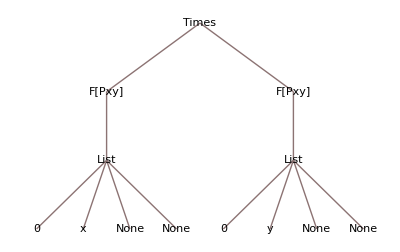

```mathematica
rels2[[2]][[1]]//TreeForm
```

```mathematica
SplitFxy[rels2[[1]]]
```

comps={-1,y,-1,y}

```mathematica
lhs=rels2[[1]][[1]]
```

```mathematica
lhs//Cases[Longest[a__]b__/;FreeQ[Times[a],y] ->a]
lhs2=F[A][{y,0,None,None}]F[B][{y,0,0,None}]F[C][{x,0,0,None}]
```

{}

```mathematica
RSolve[{a[n+1]-a[n]==x n +y n^2,a[0]==1},a[n],n]
```

{{a[n]→1/6 (6-3 n x+3 n^2 x+n y-3 n^2 y+2 n^3 y)}}

```mathematica
rels2[[2]]
```

F_Pxy[0,x]=η_2^x

```mathematica
Subscript[F, A][y,0] Subscript[F, B][y,0,0]
```

F_A[y,0] F_B[y,0,0]

```mathematica
pat=Longest[a__] b__/;(FreeQ[Times[a],y]&&FreeQ[Times[a],z]);
compsLhs=Cases[rels2[[2]][[1]],pat:>Sequence[Times[a],Times[b]],{0,1}]
```

{F_Pxy[0,x],F_Pxy[0,y]}

```mathematica
etaAssoc
```

<|η_1→1,η_3→η_2|>

```mathematica
rels2[[1]]//FullForm
```

Equation[F[Pxy][List[0,x,None,None]],Power[\[Eta][2],x]]

```mathematica
AlreadySolved[Equation[(t1_?IfFOrInvF)[{x_,y_,z_,slat_}],rhs_]]:=True
AlreadySolved[x_]:=False
```

```mathematica
MatchQ[Equation[rels2[[1]][[1]],rels2[[1]][[2]]],Equation[(t1_?IfFOrInvF)[{x_,y_,z_,slat_}],rhs_]]
```

False

```mathematica
MatchQ[rels2[[2]],rhs_]
```

True

```mathematica
MatchQ[rels2[[1]],Equation[(t1_?IfFOrInvF)[{x_,y_,z_,slat_}],rhs_]]
```

False

```mathematica
rels2[[1]]//FullForm
```

Equation[F[Pxy][List[0,x,None,None]],Power[\[Eta][2],x]]

```mathematica
rels2[[1]]
```

F_Pxy[0,x]=η_2^x

```mathematica
AlreadySolved[rels2[[1]]]
```

False

```mathematica
AlreadySolved[rels2[[1]]]
```

False

```mathematica
getFSubstitutors[rels2[[5]]]
```

```mathematica
RuleFromSolved[HoldPattern[Equation[(t1_?IfFOrInvF)[{x1_,y1_,z1_,s1_}],rhs_]]]:=Module[{x1n,y1n,x2n,y2n,rule1,rule2,rule3,rule4,svar,subrules,PattFunc},
svar[0]=0;
svar[Plus[Times[x,m_:1],k_:0]]:=a;
svar[Plus[Times[y,m_:1],k_:0]]:=b;
svar[Plus[Times[z,m_:1],k_:0]]:=c;
svar[m_]:=m;
subrules[Plus[Times[x,m_:1],k_:0]]:=x->m^-1 (a-k);
subrules[Plus[Times[y,m_:1],k_:0]]:=y->m^-1 (b-k);
subrules[Plus[Times[z,m_:1],k_:0]]:=y->m^-1 (c-k);
subrules[0]=Nothing;
subrules[x_Integer]=Nothing;
subrules[None]:=Nothing;
Print[subrules[x1]];
Print[subrules[y1]];
Print[subrules[z1]];
PattFunc[None]:=None;
PattFunc[0]:=0;
PattFunc[m_/;MemberQ[slatList,m]]:=m;
PattFunc[x_]:=Pattern[x,_];
If[MatchQ[t1,Inv[A_]],rule1=Inv[t1][PattFunc/@{svar[x1],svar[y1],svar[z1],s1}]->((rhs^-1)/.{subrules[x1],subrules[y1],subrules[z1]}),rule1=t1[PattFunc/@{svar[x1],svar[y1],svar[z1],s1}]->(rhs/.{subrules[x1],subrules[y1],subrules[z1]})];

List[rule1]]

AlreadySolved[Equation[(t1_?IfFOrInvF)[x_,y_,z_],rhs_]]:=True
AlreadySolved[x_]:=False
```

```mathematica
RuleFromSolved[Equation[(t1_?IfFOrInvF)[x_,y_,z_],rhs_]]
```

```mathematica
ReduceF[rels2[[1]]]
```

Nothing

```mathematica
l={x,-y,-x+z,1,z+1}
```

{x,-y,-x+z,1,1+z}

```mathematica
Level[l,{-1}]
```

{x,-1,y,-1,x,z,1,1,z}

```mathematica
p^(x y) q^x r^(x+y)
```

p^(x y) q^x r^(x+y)

```mathematica
Log[exp]//Series[x,y]
```

Series::sspec: y is not a valid expansion point specification.

```mathematica
Series[Log[exp],{x,0,10},{y,0,10}]
```

(Log[r] y+O[y]^11)+((Log[q]+Log[r])+Log[p] y+O[y]^11) x+O[x]^11

```mathematica
Exp[Log[r] y]
```

```mathematica
ClearAll[texp,expExpand]
exp=p^(x y)q^x r^(x+y);
rg=Distribute[{Range[0,5],Range[0,5]},List];
coeffs=SeriesCoefficient[Log[exp],{x,0,#[[1]]},{y,0,#[[2]]}]&/@rg;
coeffs
tab=Integrate[x0^#[[1]] y^#[[2]] ,{x0,0,x}]&/@rg
Print[Length[coeffs]," ",Length[tab]];
SetAttributes[expExpand, HoldAllComplete];
texp[Times[a_,x_Plus]]:=Times@@texp/@(Times[a,#]&/@x);
texp[Times[x_Plus]]:=Times@@texp/@x;
(*expExpand[ex_]:=ReleaseHold[Hold[ex]/.Exp[x_]:>texp[x]];*)
expExpand[ex_]:=ex/.Exp[x_]:>texp[x]/.{texp->Exp};
MapThread[Times,{coeffs,tab}]
expExpand@Exp@Total@(MapThread[Times,{coeffs,tab}])
```

{0,Log[r],0,0,0,0,Log[q]+Log[r],Log[p],0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

{x,x y,x y^2,x y^3,x y^4,x y^5,x^2/2,(x^2 y)/2,(x^2 y^2)/2,(x^2 y^3)/2,(x^2 y^4)/2,(x^2 y^5)/2,x^3/3,(x^3 y)/3,(x^3 y^2)/3,(x^3 y^3)/3,(x^3 y^4)/3,(x^3 y^5)/3,x^4/4,(x^4 y)/4,(x^4 y^2)/4,(x^4 y^3)/4,(x^4 y^4)/4,(x^4 y^5)/4,x^5/5,(x^5 y)/5,(x^5 y^2)/5,(x^5 y^3)/5,(x^5 y^4)/5,(x^5 y^5)/5,x^6/6,(x^6 y)/6,(x^6 y^2)/6,(x^6 y^3)/6,(x^6 y^4)/6,(x^6 y^5)/6}

36 36

{0,x y Log[r],0,0,0,0,1/2 x^2 (Log[q]+Log[r]),1/2 x^2 y Log[p],0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

p^((x^2 y)/2) q^(x^2/2) r^(x^2/2+x y)

```mathematica
exp2=Exp[0.5(Log[q]+Log[p])]
```

ⅇ^(0.5 (Log[p]+Log[q]))

```mathematica
exp2/.{E^x_->texp[x]}/.{texp->Exp}
```

p^0.5 q^0.5

```mathematica
Power[E,E^x_]
```

```mathematica
exp2//FullForm
```

```mathematica
texp[x+y]
```

texp[x] texp[y]

```mathematica
Cases[{exp2},E^x_->texp[x]]
```

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

{{TerminatedEvaluation[RecursionLimit]}}

```mathematica
ReleaseHold[Hold[exp2]/.{E^x_:>texp[x]}]
```

ⅇ^(0.5 (Log[p]+Log[q]))

```mathematica
exp2//FullForm
```

Power[E,Times[0.5,Plus[Log[p],Log[q]]]]

```mathematica
expExpand[exp]
```

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

ⅇ^(0.5 (Log[p]+Log[q]))

```mathematica
Exp[0.5 x^2( Log[q])]Exp[x^2 Log[r]]
```

q^(0.5 x^2) r^(x^2)

```mathematica
Table[Integrate[x0^i y0^j ,{x0,0,x}],{i,0,5},{j,0,5}]
```

{{x,x y0,x y0^2,x y0^3,x y0^4,x y0^5},{x^2/2,(x^2 y0)/2,(x^2 y0^2)/2,(x^2 y0^3)/2,(x^2 y0^4)/2,(x^2 y0^5)/2},{x^3/3,(x^3 y0)/3,(x^3 y0^2)/3,(x^3 y0^3)/3,(x^3 y0^4)/3,(x^3 y0^5)/3},{x^4/4,(x^4 y0)/4,(x^4 y0^2)/4,(x^4 y0^3)/4,(x^4 y0^4)/4,(x^4 y0^5)/4},{x^5/5,(x^5 y0)/5,(x^5 y0^2)/5,(x^5 y0^3)/5,(x^5 y0^4)/5,(x^5 y0^5)/5},{x^6/6,(x^6 y0)/6,(x^6 y0^2)/6,(x^6 y0^3)/6,(x^6 y0^4)/6,(x^6 y0^5)/6}}

```mathematica
Table[Integrate[x^i y^j ,{x,0,1}],{i,0,5},{j,0,5}]
```

{{1,y,y^2,y^3,y^4,y^5},{1/2,y/2,y^2/2,y^3/2,y^4/2,y^5/2},{1/3,y/3,y^2/3,y^3/3,y^4/3,y^5/3},{1/4,y/4,y^2/4,y^3/4,y^4/4,y^5/4},{1/5,y/5,y^2/5,y^3/5,y^4/5,y^5/5},{1/6,y/6,y^2/6,y^3/6,y^4/6,y^5/6}}

```mathematica
RSolve[a[x]-a[x-1],a[x],exp]
```

RSolve::dsvar: p^(x y) q^x r^(x+y) cannot be used as a variable.

RSolve[-a[-1+x]+a[x],a[x],p^(x y) q^x r^(x+y)]

```mathematica
Distribute[Range[10],Range[10],List]
```

{1,2,3,4,5,6,7,8,9,10}[{1,2,3,4,5,6,7,8,9,10}]

```mathematica
Distribute[{Range[0,5],Range[0,5]},List]
```

{{0,0},{0,1},{0,2},{0,3},{0,4},{0,5},{1,0},{1,1},{1,2},{1,3},{1,4},{1,5},{2,0},{2,1},{2,2},{2,3},{2,4},{2,5},{3,0},{3,1},{3,2},{3,3},{3,4},{3,5},{4,0},{4,1},{4,2},{4,3},{4,4},{4,5},{5,0},{5,1},{5,2},{5,3},{5,4},{5,5}}

```mathematica
Exponent[Log[exp],y]
```

0

```mathematica
Log[exp]//Expand
```

Log[p^(x y) q^x r^(x+y)]

```mathematica
Sum[x^5,{x,0,a}]
```

1/12 a^2 (1+a)^2 (-1+2 a+2 a^2)